```mathematica
A=170;
deltaE[delta_,n_,l_,j_,k_]:=-2/3*41*A^(-1/3)(n+3/2)*delta*((3 k^2-j(j+1))(3/4-j(j+1)))/((2j-1)j(j+1)(2j+3));
(* Example for i(13/2) orbit *)
N0=5;
delta0=0.22;
l=6;
j=6.5;
deltaTablej132=Table[{x,deltaE[delta0,N0,l,j,x]},{x,0.5,j,1}];
deltaTablej92=Table[{x,deltaE[delta0,N0,5,4.5,x]},{x,0.5,4.5,1}];
deltaTablej132
deltaTablej92
```

{{0.5,-1.73681},{1.5,-1.51971},{2.5,-1.08551},{3.5,-0.434202},{4.5,0.434202},{5.5,1.51971},{6.5,2.82232}}

{{0.5,-1.71049},{1.5,-1.28287},{2.5,-0.427624},{3.5,0.855247},{4.5,2.56574}}

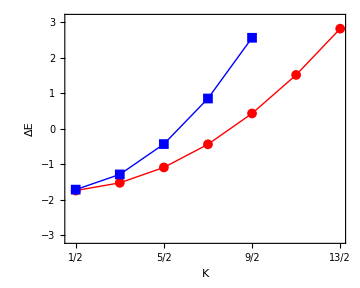

```mathematica
p=ListPlot[{deltaTablej132,deltaTablej92},ImageSize->Medium,Joined->True,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"K","ΔE"},LabelStyle->{21,Bold,Black,FontFamily->"Times"},FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{Table[k,{k,1/2,13/2,1}],Automatic}},PlotRange->{Full,{-3.1,3.1}}];
Show[p]
```

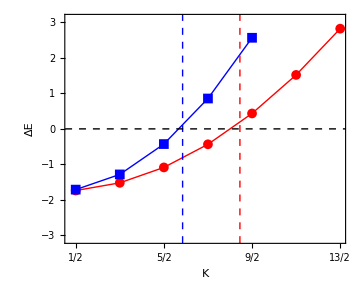

```mathematica
Show[{p,Graphics[{Blue,Dashed,Line[{{0.65*4.5,-4},{0.65*4.5,4}}]}],Graphics[{Dashed,Red,Line[{{0.65*j,-4},{0.65*j,4}}]}],Graphics[{Dashed,Black,Thick,Line[{{-1,0},{8,0}}]}]}]
```